The theoretical modeling used for our paper “Strong Reverse Saturation and Fast-Light in Ruby, Akbar Safari, et al., https://arxiv.org/abs/2301.13300”, Optics Letters 2024. See the paper for more details.

Theoretical model considering all 4 levels (not necessary)

## About

Here I am using a complete model for transitions in ruby, i.e. considering all 4 energy levels. 

Here I had not realized that the lifetime of the excited state is negligible. When considering this fact, there would be no need to use 3 rate equations; only one equation would be enough, which is what Bob uses in “Boyd - Saturation and inverse-saturation of Alexandrite (1984).pdf”. This is what I do in the next section “Simplified theoretical model”. 

We don’t need the fit model used in this section because the simplified theoretical model is already simple and analytic.

## Fitting a simple model for reverse saturation of absorption

### Explanation

```mathematica
-Graphics-

-Graphics-
```

### Fitting parameters to experimental data

First I tried to use Manipulate to find the parameters α0, β, and Is. However, it was super slow and crashing all the time. So, I decided to change these numbers by hand to find a good fit.

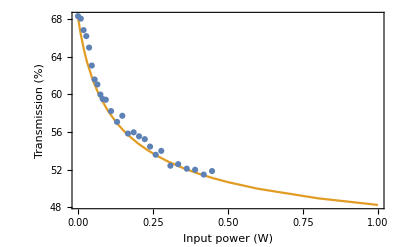

```mathematica
Clear["Global`*"]

RubyIn=92.5/100{483,453,422,392,361,333,300,280,259.7,240.6,220,200.5,180,159.6,140.7,119.1,100.1,89,80.7,70,60,49.8,39.9,29.9,20.16,10.08,55. 10^-3} 10^-3; (* about 7.5% of light is reflected from the input face of ruby. So, the power inside is 92.5% of the measured power. *)
RubyOutNoFilter=(107.5/100 106/100){203.3,189.3,178.1,165.8,154.1,141.7,131.5,121.8,114.8,107.9,99.2,91.1,81.6,74.8,65.2,56.3,48.3,43,39.3,34.7,30,25.5,21.05,16.07,10.94,5.57,30.51 10^-3}10^-3; (* 7.5% is relected from the output face of ruby and 6% is reflected from the last uncoated lens. So, I should add these losses to compensate for these losses that are not due to absorption. *)
RubyT=Transpose[{RubyIn,RubyOutNoFilter}];

TransmExp=RubyT⟦All,2⟧/RubyT⟦All,1⟧100;
TransmExp=Transpose[{RubyT⟦All,1⟧,TransmExp}];


mm=10^-3;
μm=10^-6;
nm=10^-9;

α0=19.1;
β=22.;
Is=12 10^6;  (* I guess the saturation intensity to be around the intensity of the input beam at medium power. *)


λ=473nm;
w0=36μm; (* the beam waist as measured with the camera. *)
L=20.mm;


dz=0.1mm;
z=Table[i,{i,0.,L,dz}];

z0=8mm; (* The laser was focused 8mm inside the crystal. *)

Pin={0.001,0.1,0.5,1,5,10,20,30,50,70,100,130,150,170,200,230,260,300,350,400,450,500(*,600,800,1000*)} 10^-3;
Int1=Outer[Times,Pin,ⅇ^(-α0 z)/(π w0^2(1+6((λ (z-z0))/(π w0^2))^2))]; (* This is a list that gives intensity along ruby for the first iteration for different Pin; the first sublist is for the first Pin, etc. *)
α1=α0+β/(1+Is/Int1); (* This is a list that gives absorption coefficient along ruby for the first iteration for different Pin. *)

(* 2nd iteration: *)
αzIntegral2=dz Accumulate/@α1; (* This is integral of α over z, but as a list. *)
Int2=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral2)/(π w0^2));  (* Here I wanted {a,b}*{{1,2},{3,5}}={{1a,2b},{3a,5b}} and this is how I got it! *)
α2=α0+β/(1+Is/Int2);

(* 3rd iteration: *)
αzIntegral3=dz Accumulate/@α2; (* This is integral of α over z, but as a list. *)


Pout=Pin ⅇ^(-Flatten@(Take[#,{-2}]&/@αzIntegral3)); (* Take[αzIntegral3,{-2}] gives the integral of α over z until the end of the crystal. The reason that I take the 2nd last element is that the integral is taken until L+dz. *)

TModel=Pout/Pin 100;
TModel=Transpose[{Pin,TModel}];


ListPlot[{TransmExp,TModel},Frame->True,PlotRange->All,FrameLabel->{"Input power (W)","Transmission (%)"},Joined->{False,True},FrameStyle->Directive[Black,14]]
```

## Solving the rate equations

Here I solve the rate equations  to find the absorption coefficient as a function of intensity. I assume these quantities are known from the literature: T2, T3, T4, the g factors, σ1, and σ3.

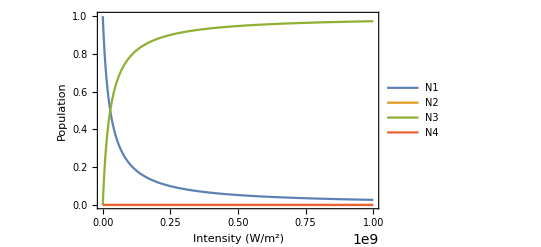

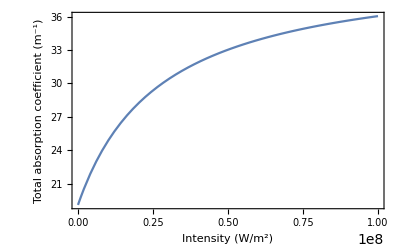

```mathematica
(*Clear["Global`*"]*)
g1=4; (* from Brik's book. *)
g2=6;
g3=4;
g4=6;
(*g1=1;
g2=1;
g3=1;
g4=1;*)

T3= 4.5 10^-3; 
T2=1. 10^-12;
T4=1. 10^-12; 

aa=2.6; (* I use this parameter to change σ1 such that σ1*NN which gives α0 remains constant. *)
NN=1/aa 1.47 10^25;  
ω=3. 10^8 (2π)/(473 10^-9);
ℏ=1.054 10^-34;
σ1=aa 1.3 10^-20 10^-4;
σ3=1.5×4.8 10^-20 10^-4;  


σ1ℏω=σ1/(ℏ ω);
σ3ℏω=σ3/(ℏ ω);
Clear[N1,N2,N3,N4]
sol=Solve[0==-σ1ℏω Int N1+g1/g2 σ1ℏω Int N2+N3/T3&&
0==σ1ℏω Int N1-g1/g2 σ1ℏω Int N2-N2/T2&&
0== N2/T2-N3/T3+N4/T4-σ3ℏω Int N3+g3/g4 σ3ℏω Int N4&&
NN==N1+N2+N3+N4,
{N1,N2,N3,N4}];  (* σ1ℏω =  σ1/ℏω*)

N1[Int_]=N1/.sol⟦1⟧;
N2[Int_]=N2/.sol⟦1⟧;
N3[Int_]=N3/.sol⟦1⟧;
N4[Int_]=N4/.sol⟦1⟧;

αTotal[Int_]=σ1(N1[Int]-g1/g2 N2[Int])+σ3(N3[Int]-g3/g4 N4[Int]);


Plot[{N1[Int]/NN,N2[Int]/NN,N3[Int]/NN,N4[Int]/NN},{Int,0,10^9},PlotRange->All,Frame->True,PlotLegends->{"N1","N2","N3","N4"}, FrameLabel->{"Intensity (W/m^2)","Population"},FrameStyle->Directive[Black,14]]

p1=Plot[(*10^-2*)αTotal[Int],{Int,0,10^8},PlotRange->All,Frame->True, FrameLabel->{"Intensity (W/m^2)","Total absorption coefficient (m^-1)"},FrameStyle->Directive[Black,14]]
```

Difference between using different degeneracy factors are shown below:

```mathematica
Show[p1,p2]
```

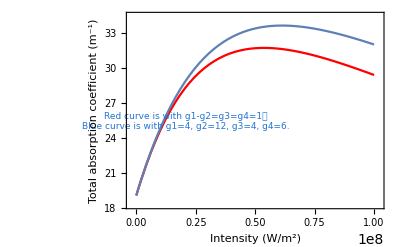

## Theoretical transmission curve

Now that I know the theoretical absorption coefficient from the previous section, I need to use that to find the transmission as a function of laser power. Then I can compare it to my experimental data. 

Since diffraction and absorption reduce the intensity, and intensity changes the absorption, I have to use either split-step, or an iterative approach. Since I used iterative above, I will use that again here.

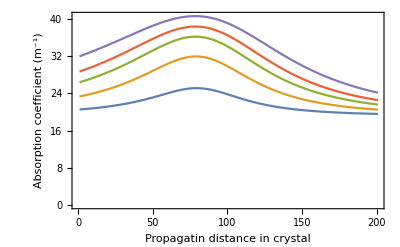

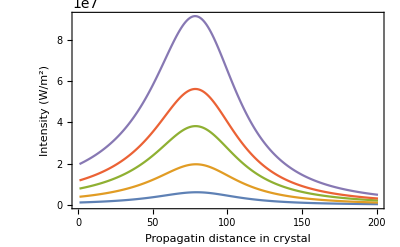

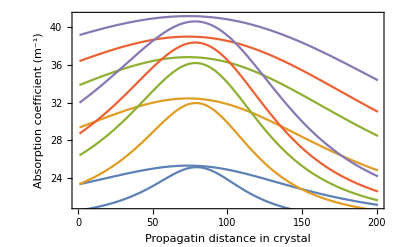

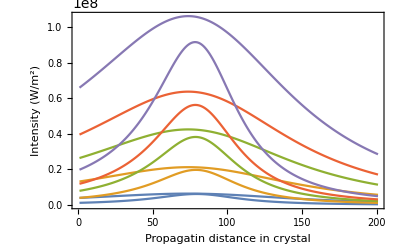

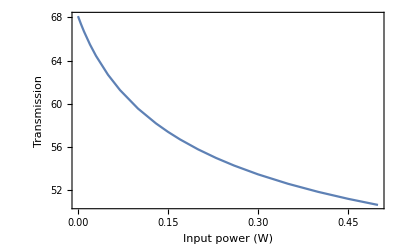

```mathematica
mm=10^-3;
μm=10^-6;
nm=10^-9;


λ=473nm;
w0=36 μm; (* the beam waist as measured *)
L=20.mm;
α0=σ1 NN;

dz=0.1mm;
z0=8mm;
z=Table[i,{i,0.,L,dz}];

Pin={0.001,0.1,0.5,1,5,10,20,30,50,70,100,130,150,170,200,230,260,300,350,400,450,500(*,600,800,1000*)} 10^-3;
int=Outer[Times,Pin,ⅇ^(-α0 z)/(π w0^2(1+((λ (z-z0))/(π w0^2))^2))]; (* This is a list that gives intensity along ruby for the first iteration for different Pin; the first sublist is for the first Pin, etc. *)

(* Plots for the first iteration: *)
p1=ListPlot[αTotal[int]⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Absorption coefficient (m^-1)"}];
in1=ListPlot[int⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Intensity (W/m^2)"}];


(* The second iteration: *)
αzIntegral1=dz Accumulate/@αTotal[int]; (* This is integral of α over z, but as a list. *)
int2=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral1)/(π w0^2));  

(* The third iteration: *)
αzIntegral2=dz Accumulate/@αTotal[int2]; (* This is integral of α over z, but as a list. *)
int3=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral2)/(π w0^2));  
p3=ListPlot[αTotal[int3]⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Absorption coefficient (m^-1)"}]
in3=ListPlot[int3⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Intensity (W/m^2)"}]


(*(* The 4th iteration: *)
αzIntegral3=dz Accumulate/@αTotal[int3]; (* This is integral of α over z, but as a list. *)
int4=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@(Pin ⅇ^-αzIntegral3)/(π w0^2);  
p4=ListPlot[αTotal[int4]⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Absorption coefficient (m^-1)"}];
in4=ListPlot[int4⟦{8,11,15,18,22}⟧,Joined->True,Frame->True,PlotRange->All,FrameStyle->Directive[Black,14],FrameLabel->{"Propagatin distance in crystal","Intensity (W/m^2)"}];*)

Show[p1,p3]
Show[in1,in3]
(* These results show that three iterations would be enough. *)

Pout=int3⟦All,-1⟧ π w0^2(1+6((λ (z⟦-1⟧-z0))/(π w0^2))^2);
TransmTh=Transpose[{Pin,Pout/Pin 100}];
T1=ListPlot[TransmTh,Joined->True,Frame->True,FrameLabel->{"Input power (W)","Transmission"},FrameStyle->Directive[Black,14]]
```

## Fitting Theory to experiment

Here I have combined the codes of the past two sections to plot them together. 

To fit the theoretical curve to the experimental data, I change these parameter:
T3
T4
σ3

These are shown in red in the code. These numbers are taken from some references, but I multiply them by a factor to change them.

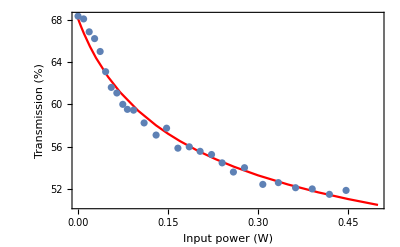

```mathematica
(*Clear["Global`*"]*)

RubyIn=92.5/100{483,453,422,392,361,333,300,280,259.7,240.6,220,200.5,180,159.6,140.7,119.1,100.1,89,80.7,70,60,49.8,39.9,29.9,20.16,10.08,55. 10^-3} 10^-3; (* about 7.5% of light is reflected from the input face of ruby. So, the power inside is 92.5% of the measured power. *)
RubyOutNoFilter=(107.5/100 106/100){203.3,189.3,178.1,165.8,154.1,141.7,131.5,121.8,114.8,107.9,99.2,91.1,81.6,74.8,65.2,56.3,48.3,43,39.3,34.7,30,25.5,21.05,16.07,10.94,5.57,30.51 10^-3}10^-3; (* 7.5% is relected from the output face of ruby and 6% is reflected from the last uncoated lens. So, I should add these losses to compensate for these losses that are not due to absorption. *)
RubyT=Transpose[{RubyIn,RubyOutNoFilter}];

TransmExp=RubyT⟦All,2⟧/RubyT⟦All,1⟧100;
TransmExp=Transpose[{RubyT⟦All,1⟧,TransmExp}];




g1=4; (* from Brik's book. *)
g2=6;
g3=4;
g4=6;

ω=3. 10^8 (2π)/(473 10^-9);
ℏ=1.054 10^-34;
T2=1. 10^-12;
T4=1. 10^-12; 

T3= 5 10^-3; 
aa=3.1; (* I use this parameter to change σ1 such that σ1*NN which gives α0 remains constant. *)
NN=1/aa 1.47 10^25;  
σ1=aa 1.3 10^-20 10^-4; 
σ3=2×4.8 10^-20 10^-4;  


σ1ℏω=σ1/(ℏ ω);
σ3ℏω=σ3/(ℏ ω);
Clear[N1,N2,N3,N4]
sol=Solve[0==-σ1ℏω Int N1+g1/g2 σ1ℏω Int N2+N3/T3&&
0==σ1ℏω Int N1-g1/g2 σ1ℏω Int N2-N2/T2&&
0== N2/T2-N3/T3+N4/T4-σ3ℏω Int N3+g3/g4 σ3ℏω Int N4&&
NN==N1+N2+N3+N4,
{N1,N2,N3,N4}];  (* σ1ℏω =  σ1/ℏω*)

N1[Int_]=N1/.sol⟦1⟧;
N2[Int_]=N2/.sol⟦1⟧;
N3[Int_]=N3/.sol⟦1⟧;
N4[Int_]=N4/.sol⟦1⟧;

αTotal[Int_]=σ1(N1[Int]-g1/g2 N2[Int])+σ3(N3[Int]-g3/g4 N4[Int]);



mm=10^-3;
μm=10^-6;
nm=10^-9;


λ=473nm;
w0=36μm; (* the beam waist radius as measured *)
L=20.mm;
α0=σ1 NN;

dz=0.1mm;
z0=8mm;
z=Table[i,{i,0.,L,dz}];

Pin={0.001,0.1,0.5,1,5,10,20,30,50,70,100,130,150,170,200,230,260,300,350,400,450,500(*,600,800,1000*)} 10^-3;
int=Outer[Times,Pin,ⅇ^(-α0 z)/(π w0^2(1+6((λ (z-z0))/(π w0^2))^2))]; (* This is a list that gives intensity along ruby for the first iteration for different Pin; the first sublist is for the first Pin, etc. *)


(* The second iteration: *)
αzIntegral1=dz Accumulate/@αTotal[int]; (* This is integral of α over z, but as a list. *)
int2=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral1)/(π w0^2));  

(* The third iteration: *)
αzIntegral2=dz Accumulate/@αTotal[int2]; (* This is integral of α over z, but as a list. *)
int3=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral2)/(π w0^2));  

(* These results show that even no iteration (considering only linear absorption and diffraction) is good enough in most cases to calculate the intensity and absorption coefficient along the length of he crystal. And for the case of high intensities three iterations would be more than enough. *)

Pout=int3⟦All,-1⟧ π w0^2(1+6((λ (z⟦-1⟧-z0))/(π w0^2))^2);
TransmTh=Transpose[{Pin,Pout/Pin 100}];

p2=Show[ListPlot[TransmTh,Joined->True,Frame->True,FrameLabel->{"Input power (W)","Transmission (%)"},FrameStyle->Directive[Black,14],PlotRange->All,PlotStyle->Red],
ListPlot[TransmExp,Joined->False,Frame->True,FrameLabel->{"Input power (W)","Transmission (%)"},FrameStyle->Directive[Black,14]],PlotRange-> All]
```

Simplified theoretical model

## Fitting theory to experiment

```mathematica
Clear["Global`*"]
```

```mathematica
RubyIn=92.5/100{483,453,422,392,361,333,300,280,259.7,240.6,220,200.5,180,159.6,140.7,119.1,100.1,89,80.7,70,60,49.8,39.9,29.9,20.16,10.08,55. 10^-3} 10^-3; (* about 7.5% of light is reflected from the input face of ruby. So, the power inside is 92.5% of the measured power. *)
RubyOutNoFilter=(107.5/100 106/100){203.3,189.3,178.1,165.8,154.1,141.7,131.5,121.8,114.8,107.9,99.2,91.1,81.6,74.8,65.2,56.3,48.3,43,39.3,34.7,30,25.5,21.05,16.07,10.94,5.57,30.51 10^-3}10^-3; (* 7.5% is relected from the output face of ruby and 6% is reflected from the last uncoated lens. So, I should add these losses to compensate for these losses that are not due to absorption. *)
RubyT=Transpose[{RubyIn,RubyOutNoFilter}];

TransmExp=RubyT⟦All,2⟧/RubyT⟦All,1⟧100;
TransmExp=Transpose[{RubyT⟦All,1⟧,TransmExp}];

ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34;


T3= 5.0 10^-3; 
aa=3.1;
NN=1/aa 1.47 10^25;  
σ1=aa 1.3 10^-20 10^-4; 
σ3=2×4.8 10^-20 10^-4;  

σ1ℏω=σ1/(ℏ ω);  σ3ℏω=σ3/(ℏ ω);
αTotal[Int_]=(σ1-σ3)NN/(1+T3 Int σ1ℏω)+σ3 NN;

mm=10^-3;  μm=10^-6;  nm=10^-9;  λ=473nm;
w0=36μm; (* the beam waist radius as measured *)
L=20.mm;  α0=σ1 NN;

dz=0.1mm;  z0=8mm;
z=Table[i,{i,0.,L,dz}];

Pin={0.001,0.1,0.5,1,5,10,20,30,50,70,100,130,150,170,200,230,260,300,350,400,450,500(*,600,800,1000*)} 10^-3;
int=Outer[Times,Pin,ⅇ^(-α0 z)/(π w0^2(1+6((λ (z-z0))/(π w0^2))^2))]; (* This is a list that gives intensity along ruby for the first iteration for different Pin; the first sublist is for the first Pin, etc. *)


(* The second iteration: *)
αzIntegral1=dz Accumulate/@αTotal[int]; (* This is integral of α over z, but as a list. *)
int2=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral1)/(π w0^2));  

(* The third iteration: *)
αzIntegral2=dz Accumulate/@αTotal[int2]; (* This is integral of α over z, but as a list. *)
int3=1/(1+6((λ (z-z0))/(π w0^2))^2)#&/@((Pin ⅇ^-αzIntegral2)/(π w0^2));  

(* These results show that even no iteration (considering only linear absorption and diffraction) is good enough in most cases to calculate the intensity and absorption coefficient along the length of he crystal. And for the case of high intensities three iterations would be more than enough. *)

Pout=int3⟦All,-1⟧ π w0^2(1+6((λ (z⟦-1⟧-z0))/(π w0^2))^2);
TransmTh=Transpose[{Pin,Pout/Pin 100}];

p1=Show[ListPlot[TransmTh,Joined->True,Frame->True,FrameLabel->{"Input power (W)","Transmission (%)"},FrameStyle->Directive[Black,14],PlotRange->All,PlotStyle->Red],
ListPlot[TransmExp,Joined->False,Frame->True,FrameLabel->{"Input power (W)","Transmission (%)"},FrameStyle->Directive[Black,14]],PlotRange-> All]
```

-Graphics-

-Graphics-

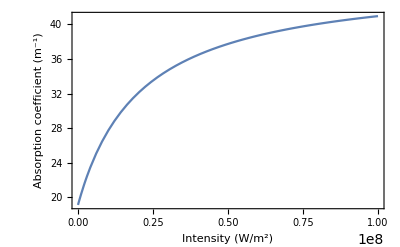

```mathematica
Plot[αTotal[Int],{Int,0,10^8},Frame->True,FrameLabel->{"Intensity (W/m^2)","Absorption coefficient (m^-1)"},FrameStyle->Directive[Black,14],PlotRange-> All]
```

## Plotting probe absorption assuming hole burning

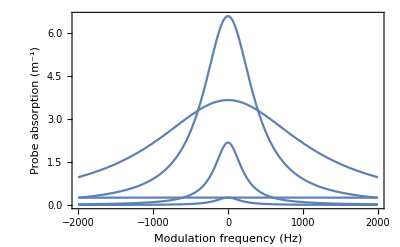

```mathematica
Is=(ℏ ω)/(σ1 T3);
I0={0.01,0.1,1,5,100}Is;

Plot[Re[(*NN/(1+I0/Is)(σ1-σ3)+σ3 NN*)-(σ1-σ3)NN (I0/Is)/(1+I0/Is)(1+I0/Is+ⅈ Ω T3)/((1+I0/Is)^2+(Ω T3)^2)],{Ω,-2000,2000},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"Modulation frequency (Hz)","Probe absorption (m^-1)"},FrameStyle->Directive[Black,14]]
```

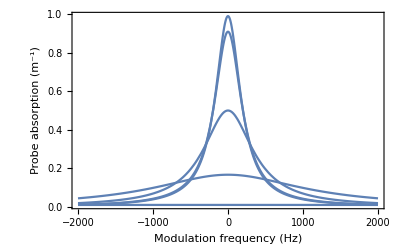

```mathematica
Plot[Re[(1+I0/Is+ⅈ Ω T3)/((1+I0/Is)^2+(Ω T3)^2)],{Ω,-2000,2000},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"Modulation frequency (Hz)","Probe absorption (m^-1)"},FrameStyle->Directive[Black,14]]
```

## A simple model

This model represents my final thought on this matter. We simply need to solve the time-dependent rate equation and find the population as a function of time for a modulated input intensity. We see below that the population, and consequently the absorption, lags behind the driving intensity. This explains the apparent pulse advancement very nicely.

Below, I assume an input sinusoidal intensity modulation and find the corresponding absorption over time. Then, I simply calculate the output intensity from this lagged absorption based on I_out=I_in ⅇ^-αL. In other words, I have ignored the change in the absorption upon propagation in the crystal due to diffraction and nonlinear absorption. For a more accurate result, we can use an iterative approach. But it is not necessary for a qualitative agreement.

### Plots are fit manually

To compare different quantities, I plot them together. However, I have to change the offset and scale of one graph to make it comparable to the other graph. I do this manually here.

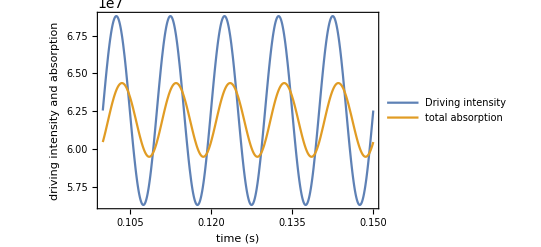

-Graphics-

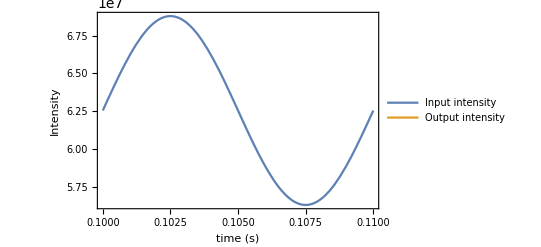

```mathematica
Clear["Global`*"]
ms=10^-3;
ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);    I0=3Is;   I1=10/100 I0;
Ω=100;

(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

tList=Table[j,{j,100.ms,150ms,0.1ms}];
maxN3=Max@N3[tList];
minN3=Min@N3[tList];
maxInt=Max@(I0+I1 Sin[2π Ω tList]);
minInt=Min@(I0+I1 Sin[2π Ω tList]);

Plot[{I0+I1 Sin[2π Ω t],(maxInt-minInt)/2( α[t]-39)+(maxInt+minInt)/2},{t,100ms,150ms},PlotRange->All,Frame->True,FrameLabel->{"time (s)","driving intensity and absorption"},FrameStyle->Directive[Black,14],PlotLegends->{"Driving intensity", "total absorption"}]

Plot[{N3[t],(maxN3-minN3)/2(α[t]-39)+(maxN3+minN3)/2},{t,100ms,150ms},PlotRange->All,Frame->True,FrameLabel->{"time (s)","Population N_3 and total absorption"},FrameStyle->Directive[Black,14],PlotLegends->{"Population N_3","Total absorption"}]

Plot[{I0+I1 Sin[2π Ω t],2.3Iout[t]-0.35 10^7},{t,100ms,110ms},PlotRange->All,Frame->True,FrameLabel->{"time (s)","Intensity"},FrameStyle->Directive[Black,14],PlotLegends->{"Input intensity","Output intensity"}]
```

### Plots are fit automatically

I have scaled the graphs to fit them in one plot automatically. But I cannot use legends here.

#### Input intensity and absorption

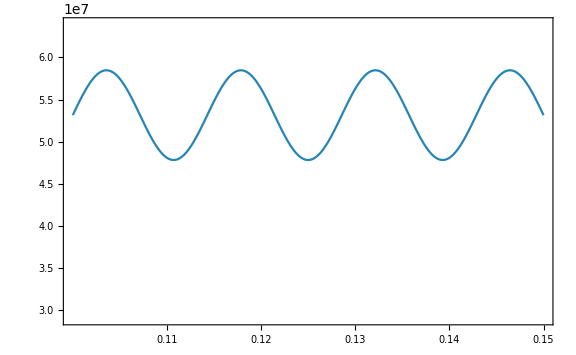
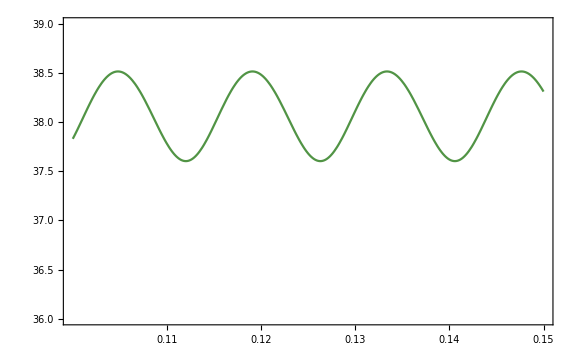

```mathematica
Clear["Global`*"]
ms=10^-3;
ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);    I0=2.55Is;   I1=10/100 I0;
Ω=70;

(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

p1=Plot[I0+I1 Sin[2π Ω t],{t,100ms,150ms},PlotRange->{2.9 10^7,6.4 10^7},PlotStyle->RGBColor[0.145098, 0.521569, 0.705882],ImagePadding->60,Axes->False,Frame->{True,False,False,True},FrameTicks->{{None,All},{All,None}},FrameStyle->{Automatic,Automatic,Automatic,RGBColor[0.145098, 0.521569, 0.705882]},ImageSize->Large];

p2=Plot[α[t],{t,100ms,150ms},PlotRange->{36,39},Frame->True,PlotStyle->RGBColor[0.317647, 0.580392, 0.270588],ImagePadding->60,Frame->{True,True,True,False},FrameStyle->{Automatic,RGBColor[0.317647, 0.580392, 0.270588],Automatic,Automatic},FrameTicks->{{All,None},{All,None}},ImageSize->Large];

Overlay[{p1,p2}]
```

#### Input intensity and output intensity

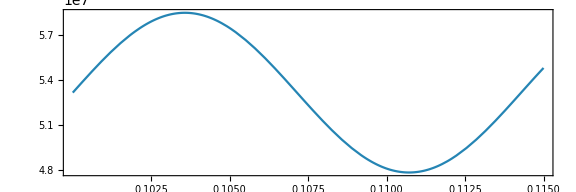

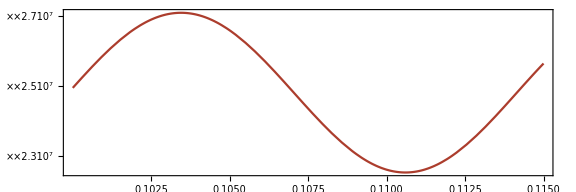

-Graphics--Graphics-

```mathematica
Clear["Global`*"]
ms=10^-3;
ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);    I0=2.55Is;   I1=10/100 I0;
Ω=70;
L=0.02; (* Length of the ruby crystal (2cm). *)

T=1/Ω; (* Period of the modulation. *)
t0=100ms;
t1=t0+T;
t1=t0+15ms;

(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

p1=Plot[I0+I1 Sin[2π Ω t],{t,t0,t1},PlotRange->All,PlotStyle->RGBColor[0.145098, 0.521569, 0.705882],ImagePadding->60,Axes->False,Frame->{True,False,False,True},FrameTicks->{{None,All},{All,None}},FrameStyle->{Automatic,Automatic,Automatic,RGBColor[0.145098, 0.521569, 0.705882]},ImageSize->Large,AspectRatio->1/3]

p2=Plot[Iout[t],{t,t0,t1},PlotRange->All,Frame->True,PlotStyle->RGBColor[0.67451, 0.239216, 0.176471],ImagePadding->60,Frame->{True,True,True,False},FrameStyle->{Automatic,RGBColor[0.67451, 0.239216, 0.176471],Automatic,Automatic},FrameTicks->{{All,None},{All,None}},ImageSize->Large,AspectRatio->1/3]

Overlay[{p1,p2}]
```

#### Calculating the shift (advancement) across the entire period

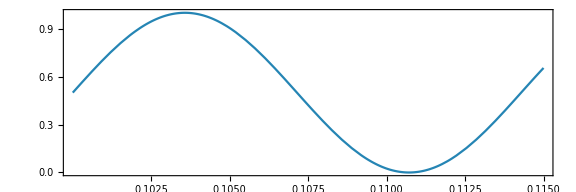
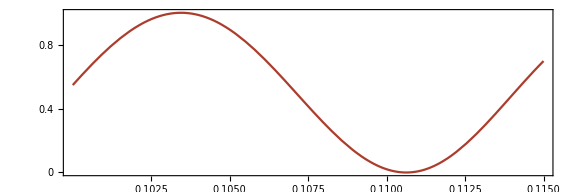

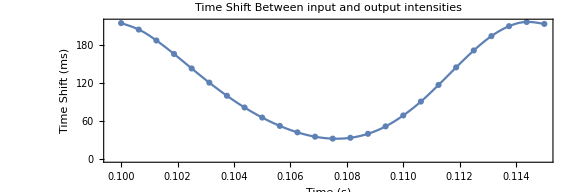

```mathematica
(*Clear["Global`*"]*)
ms=10^-3;
ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);    I0=2.55Is;   I1=50/100 I0;
Ω=70;
L=0.02;

T=1/Ω;
t0=100ms;
t1=t0+T;
t1=t0+15ms;

(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

(* Normalizing Iin and Iout. Otherwise, we cannot find their difference in time (tShift). *)
(* For Iout, I had to create a numerical list to find the min and max. *)
numPoints=1000;(*Number of points to sample*)
sampledValues=Table[{t,Iout[t]},{t,t0,t1,(t1-t0)/numPoints}];

(*Find the minimum and maximum values of the sampled data*)
Ioutmin=Min[sampledValues[[All,2]]];
Ioutmax=Max[sampledValues[[All,2]]];
IoutNormalized[t_]:=(Iout[t]-Ioutmin)/(Ioutmax-Ioutmin);

Iinmin=MinValue[{I0+I1 Sin[2π Ω t],t0<=t<=t1},t];
Iinmax=MaxValue[{I0+I1 Sin[2π Ω t],t0<=t<=t1},t];
IinNormalized[t_]:=(I0+I1 Sin[2π Ω t]-Iinmin)/(Iinmax-Iinmin);



p1=Plot[IinNormalized[t],{t,t0,t1},PlotRange->All,PlotStyle->RGBColor[0.145098, 0.521569, 0.705882],ImagePadding->60,Axes->False,Frame->{True,False,False,True},FrameTicks->{{None,All},{All,None}},FrameStyle->{Automatic,Automatic,Automatic,RGBColor[0.145098, 0.521569, 0.705882]},ImageSize->Large,AspectRatio->1/3];

p2=Plot[IoutNormalized[t],{t,t0,t1},PlotRange->All,Frame->True,PlotStyle->RGBColor[0.67451, 0.239216, 0.176471],ImagePadding->60,Frame->{True,True,True,False},FrameStyle->{Automatic,RGBColor[0.67451, 0.239216, 0.176471],Automatic,Automatic},FrameTicks->{{All,None},{All,None}},ImageSize->Large,AspectRatio->1/3];

Overlay[{p1,p2}]


(* Finding the shift between the input and output intensities, tShift: *)
dt=0.6ms; (* time step size for finding the tShift. *)
iN=Round[(t1-t0)/dt];
tShift={};

For[i=1,i<=iN,i++,
tx=t0+i dt;
dτ=1ms;(*The search interval around tx*)
(*Find the time t such that IoutNormalized[t1]=IinNormalized[tx],searching around t0+/-dτ: *)
τSolution=FindRoot[IoutNormalized[t]==IinNormalized[tx],{t,tx,tx-dτ,tx+dτ}];
τ=t/. τSolution;
AppendTo[tShift,τ-tx]
]

(*Plot the time shift as a function of t*)
P50=ListLinePlot[-tShift/10^-6,DataRange->{t0,t1},FrameLabel->{"Time (s)","Time Shift (ms)"},PlotLabel->"Time Shift Between input and output intensities",InterpolationOrder->2,PlotMarkers->Automatic,Frame->True,ImageSize->Large,AspectRatio->1/3]
```

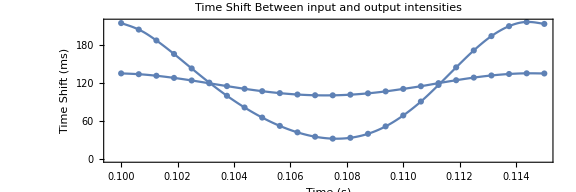

```mathematica
Show[P50,P10]
```

### Calculating the group index

We see clearly from these plots that the absorption is lagged behind the driving intensity. As a consequence, the peak of the output intensity appears before the peak of the input intensity. However, this advancement is not very clear from the plot. So, below, I am finding the positions of these peaks.

```mathematica
Clear["Global`*"]
ms=10^-3;
ω=3. 10^8 (2π)/(473 10^-9);  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);    I0=2.55Is;   I1=10/100 I0;
Ω=70;
L=0.02;

(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

tList2=Table[j,{j,100.ms,110ms,0.0001ms}];

InputIntList=I0+I1 Sin[2π Ω tList2];
maxInput=Max@InputIntList;
tin=tList2⟦Position[InputIntList,maxInput]⟦1,1⟧⟧;

OutputIntList=Iout[tList2]⟦1⟧;
maxOutput=Max@OutputIntList;
tout=tList2⟦Position[OutputIntList,maxOutput]⟦1,1⟧⟧;

Δt=tin-tout;  (* This gives the time difference between the peaks of the input intensity and the output intensity in second. *)
Print["Time advance = ", Δt 10^6," μs"]
Print["Group index = ",-3 10^8 Δt/L]
```

Time advance = 119.9 μs

Group index = -1.7985×10^6

### Calculating the group delay for different Intensities

We see clearly from these plots that the absorption is lagged behind the driving intensity. As a consequence, the peak of the output intensity appears before the peak of the input intensity. However, this advancement is not very clear from the plot. So, below, I am finding the positions of these peaks.

```mathematica
Clear["Global`*"]
ms=10^-3;
ω=3. 10^8 ((2π)/(473 10^-9));  ℏ=1.054 10^-34; 
(* I got these parameters from my transmission vs power measurement. *)
σ1=4.03 10^-24; σ3=9.6 10^-24;  σ1ℏω=σ1/(ℏ ω); NN=4.7419355 10^24;  T3=5ms;
Is=(ℏ ω)/(σ1 T3);   
Ω=70;
L=0.02;

I0List={};
ΔtList={};

For[j=1,j<250,j++,
PrintTemporary["Progress: ",j," out of 250"];
I0=0.05 j Is;   
I1=(10/100)I0;
(* This is the time dependent rate equation that I am solving numerically: *)
sol=NDSolve[{n1'[t]==-σ1ℏω n1[t] (I0+I1 Sin[2π Ω t])+(NN-n1[t])/T3,n1[0]==NN},n1,{t,0,300ms}];

N1[t_]=n1[t]/.sol;
N3[t_]=NN-N1[t];

α[t_]=σ1 N1[t]+σ3 N3[t];
Iout[t_]=(I0+I1 Sin[2π Ω t])ⅇ^(-α[t] L);

tList2=Table[j,{j,100.ms,110ms,0.0001ms}];

InputIntList=I0+I1 Sin[2π Ω tList2];
maxInput=Max@InputIntList;
tin=tList2⟦Position[InputIntList,maxInput]⟦1,1⟧⟧;

OutputIntList=Iout[tList2]⟦1⟧;
maxOutput=Max@OutputIntList;
tout=tList2⟦Position[OutputIntList,maxOutput]⟦1,1⟧⟧;

Δt=tin-tout ; (* This gives the time difference between the peaks of the input intensity and the output intensity in second. *)

AppendTo[I0List,0.05j];
AppendTo[ΔtList,Δt];
]

ΔtI0=Transpose[{I0List,ΔtList}];

ListPlot[ΔtI0,Frame->True,PlotRange->All,Joined->True,FrameLabel->{"Input intensity (Is)","Pulse advancement (s)"},FrameStyle->Directive[Black,14]]
```

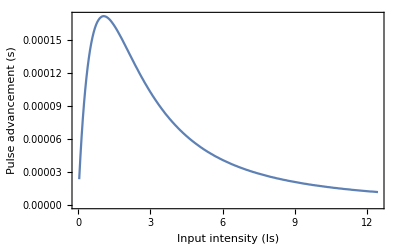

```mathematica
With 10% modulation and Ω=70:
```